```mathematica
3
```

# Iterative algorithm for computation of QFI using variational principle From paper of K. Macieszczak, arXiv:1312.1356v1

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
$PrePrint=MatrixForm;
On[Assert];
```

## Coloring description

Program info cell

Function description cell

```mathematica
(*Initialization cell*)
```

Theory cell

## Algorithm

Usage:
* In order to change quantum channel, change definition of ΛEl (and derivative).
TODO In order to change input state, change ψ_0 
* For now, input state is passed as argument in functions in Plots and analysis part of this script.

In order to change quantum channel, change definition of ΛEl (and derivative).
TODO In order to change input state, change ψ_0 
For now, input state is passed as argument in functions in Plots and analysis part of this script.

### Constants and parameters

```mathematica
(* As for now, they are quite random. *)
ω0=10.;
ωm=0.3;
(*g=0.03;*)

(* some useful states: stateN represents N-1-photonic state *)
state5={0.2,0.1ⅈ,0.3ⅈ,0.1,Sqrt[1-0.2^2-0.3^2-2*0.1^2]}//Normalize;
state10={0.2,0.1ⅈ,0.3ⅈ,0.1,0.5,0.2,0.1ⅈ,0.7ⅈ,0.5,0.05ⅈ}//Normalize;
state15={0.2,0.1ⅈ,0.3ⅈ,0.1,0.5,0.2,0.1ⅈ,0.7ⅈ,0.5,0.05ⅈ, 0.8, 0.1, 0.05ⅈ, 0.4ⅈ, 0.2}//Normalize;
```

### Functions

Functions below return ELEMENT of a density matrix after applying quantum channel.They are used only in Λ functions below.
Parameters : 
■ element - matrix element of density matrix
■ ind - indexes of this matrix element

```mathematica
(*(* From Wojtek's thesis and program *)
ΛEl[element_, ind_] := element*Exp[-ⅈ(ind[[2]]-ind[[1]])(1-f)ω0*t]*
Exp[ⅈ((g(1-2f))/ωm(ind[[2]]-1))^2(ωm t-Sin[ωm t])^2]*
Exp[-ⅈ((g(1-2f))/ωm(ind[[1]]-1))^2(ωm t-Sin[ωm t])^2]*
Exp[((g(1-2f))/ωm)^2*4*(Sin[ωm t/2])^2((ind[[2]]-1)(ind[[1]]-1)-0.5*(ind[[2]]-1)^2-0.5*(ind[[1]]-1)^2)];

(* derivative : *) (* From Wojtek's thesis and program *)
ΛprimEl[element_, ind_] := element/ωm^2 ⅇ^(((0.5-1. f)^2 g^2 (-8.000000000000002 ind[[2]]^2+16. ind[[2]] ind[[1]]-8.000000000000002 ind[[1]]^2) Sin[(t ωm)/2]^2-ⅈ (ind[[2]]-ind[[1]]) (-t ((1-2 f)^2 g^2 (-2+ind[[2]]+ind[[1]]) t+(-1+f) ω0) ωm^2-(1-2 f)^2 g^2 (-2+ind[[2]]+ind[[1]]) Sin[t ωm] (-2 t ωm+Sin[t ωm])))/ωm^2) (g^2 ((8.-16. f) ind[[2]]^2+(-16.+32. f) ind[[2]] ind[[1]]+(8.-16. f) ind[[1]]^2) Sin[(t ωm)/2]^2+ⅈ (ind[[2]]-ind[[1]]) (t (4 (-1+2 f) g^2 (-2+ind[[2]]+ind[[1]]) t+ω0) ωm^2+4 (-1+2 f) g^2 (-2+ind[[2]]+ind[[1]]) Sin[t ωm] (-2 t ωm+Sin[t ωm]))); *)


(* My version with displaced mirror state *)
(* quantum channel Λ: *) 
ΛEl[element_, ind_] := element*
Exp[-ⅈ((ind[[2]]-1)-(ind[[1]]-1))(1-f)ω0*t]*
Exp[ⅈ((g(1-2f))/ωm)^2((ind[[2]]-1)^2-(ind[[1]]-1)^2)(ωm t-Sin[ωm t])^2]*
Exp[ⅈ((g(1-2f))/ωm)^2((ind[[2]]-1)-(ind[[1]]-1))nbar Sin[ωm t]]*(* additional factor from product of displacement operators *)
Exp[((g(1-2f))/ωm)^2(((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(ⅈ ωm t))
-1/2((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[2]]-1)-((ind[[2]]-1)-nbar)ⅇ^(+ⅈ ωm t))-1/2((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(-ⅈ ωm t))((ind[[1]]-1)-((ind[[1]]-1)-nbar)ⅇ^(+ⅈ ωm t)))] (* trace *)
(* derivative : *) (* my, displaced mirror *)
ΛprimEl[element_, ind_] := D[ΛEl[element, ind],f]
```

Functions below return WHOLE density matrix after applying quantum channel.
Parameters:
■ state - state |ψ_0> which goes through quantum channel Λ

```mathematica
(* quantum channel: Λ *)
Λ[state_] := MapIndexed[ΛEl, state, {2}];
Λdag[state_] := ConjugateTranspose[Λ[state]];

(* derivative: *)
Λprim[state_] := MapIndexed[ΛprimEl, state, {2}];
Λprimdag[state_] := ConjugateTranspose[Λprim[state]];
```

Returns number operator: that is a matrix equivalent of ∑_(i=0)^(n-1) i |i><i|

```mathematica
defineNumberOperator[n_]:=Module[{i},
numberOperator=ConstantArray[0,{n,n}];
For[i=2,i≤n,i++,
numberOperator[[i]][[i]]=i-1;
];
numberOperator
]
```

CalculateQFI function returns a pair: biggest eigenvector of system calculated according to algorithm and Quantum Fisher Information of current state.
Therefore it can be used as a single step in optimal QFI calculation function as well as just calculating QFI of some state (and ignoring returned biggest eigenvector).
■ currentState - previous state if function is used as a step in optimal QFI calculation using variational principle or just any state to have calculated its QFI.

```mathematica
CalculateQFI[rules_,currentState_,initialNbar_]:=Module[{state=currentState,rls=rules,step,qfi,ρ,Λofρ,eigenSys,Λofρprim,SLD,matrix,ind, system,biggestState,k,j},
numberOperator=defineNumberOperator[Length[currentState]];
newNbar=initialNbar;
ρ = KroneckerProduct[state, Conjugate[state]];

Λofρ = Λ[ρ]/.rules;
Λofρ=Λofρ/.{nbar->newNbar};

eigenSys = Eigensystem[Λofρ];

Λofρprim=Λprim[ρ]/.rules; (* derivative *)
Λofρprim=Λofρprim/.{nbar->newNbar};

SLD = ConstantArray[0, {Length[Λofρ], Length[Λofρ]}];

(* Inner loops to calculate SLD: *)
For[k=1, k ≤ Length[Λofρ],k++,
For[j = 1, j ≤ Length[Λofρ], j++,
(* Below the purity treshold ("else") we can not add this part or calculate using simpler expression ( 2|ψ><dψ| - |dψ><dψ|) (in Wojtek's thesis *)
If[ Abs[eigenSys[[1]][[k]]+eigenSys[[1]][[j]]]>10^-6,
SLD+=2/(eigenSys[[1]][[k]]+eigenSys[[1]][[j]])*(Conjugate[eigenSys[[2]][[k]]].Λofρprim.eigenSys[[2]][[j]])*KroneckerProduct[eigenSys[[2]][[k]],Conjugate[eigenSys[[2]][[j]]]],
False (* just do nothing if false *)
]
]
];


G=-Λdag[SLD.SLD]+2.*Λprimdag[SLD]; (* generating matrix according to paper *)
G=G/.rules;
G=G/.{nbar->newNbar};
G=G//Chop;

(* Next steps prepare variables and runs maximization of <ψ|G|ψ>: we seek such |ψ>, which maximizes this expression and is constrained by <ψ|n|ψ>=nbar and <ψ|ψ>=1 *)
xs=Table[Symbol["x"<>ToString@i],{i,Length[G]}];
ys=Table[Symbol["y"<>ToString@i],{i,Length[G]}];
allvariables=Join[xs,ys];
ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[G]}];
wynik=Maximize[{Re[ψconj.G.ψ],ψconj.ψ==1 && ψconj.numberOperator.ψ==newNbar},allvariables];


biggestState=ψ/.wynik[[2]];
qfi=Tr[Λofρ.SLD.SLD];(* calculating Fisher information *)
{biggestState, qfi} (* returning new state and its qfi *)
]
```

CalculateOptimalQFI is main function of program. It returns optimal state and its Fisher information.
Parameters:
■ maxSteps - maximal number of steps performed by this algorithm to obtaining FI of state.
■ accuracy - algorithm stops after reaching this threshold
■ inputState -|ψ_(i-1)> or|ψ_0> 
REMINDER! To get only value of maximal information, take only second element from return value! [[2]]

```mathematica
CalculateOptimalQFI[rules_,maxSteps_,accuracy_,inputState_,initialNbar_] :=  Module[{state=inputState, qfi=-∞,step,newState,newQfi,SLD,L,matrix,G,k,j,Λofρ,Λofρprim,eigenSys,system,ind,i,len=Length[inputState]},
Assert[maxSteps>0];
numberOperator=defineNumberOperator[Length[inputState]];
newNbar=initialNbar;
For[step = 0, step < maxSteps, step++,
ρ = KroneckerProduct[state, Conjugate[state]];
(*Print["ρ: ", ρ//MatrixForm];*)

Λofρ = Λ[ρ]/.rules;
Λofρ=Λofρ/.{nbar->newNbar};
(*Print["Λofρ: ", Λofρ//MatrixForm];*)

(*Print["Λofρ:", Λofρ//MatrixForm];*)
eigenSys = Eigensystem[Λofρ];


Λofρprim=Λprim[ρ]/.rules; (* derivative *)
Λofρprim=Λofρprim/.{nbar->newNbar};
(*Print["Λofρprim: ", Λofρprim//MatrixForm];*)

(* OLD VERSION OF CALCULATING QFI *)
(* Inner loops to calculate SLD: *)
SLD = ConstantArray[0, {Length[Λofρ], Length[Λofρ]}];
For[k=1, k ≤ Length[Λofρ],k++,
For[j = 1, j ≤ Length[Λofρ], j++,
(* Below the purity treshold ("else") we can not add this part or calculate using simpler expression ( 2|ψ><dψ| - |dψ><dψ|) (in Wojtek's thesis *)
If[ Abs[eigenSys[[1]][[k]]+eigenSys[[1]][[j]]]>10^-6,
SLD+=2/(eigenSys[[1]][[k]]+eigenSys[[1]][[j]])*(Conjugate[eigenSys[[2]][[k]]].Λofρprim.eigenSys[[2]][[j]])*KroneckerProduct[eigenSys[[2]][[k]],Conjugate[eigenSys[[2]][[j]]]],
True
(*Print["!!! Omitting to little eigenValues in denominator"];*) (* just do nothing if false *)
]
]
];

(* NEW VERSION OF CALCULATING QFI *)
(*SLD={};
SLDvars={};
For[j=1,j≤len,j++,
xs=Table[Symbol["x"<>ToString[j]<>ToString@i],{i,len}];
ys=Table[Symbol["y"<>ToString[j]<>ToString@i],{i,len}];
SLDvars=Join[SLDvars,xs,ys];
row=Table[xs[[i]]+ⅈ*ys[[i]],{i,len}];
SLD=Append[SLD,row];
];*)


(*Print["SLD with symbolic variables:",SLD//MatrixForm];
Print["Λofρprim = ", Λofρprim//MatrixForm];
Print["Tr[Λofρprim.SLD] = ",Tr[Λofρprim.SLD]];
(*Print[2Trace[Λofρprim.SLD]-Trace[Λofρprim.SLD.SLD]];*)
wyn=Maximize[{2Trace[Λofρprim.SLD]-Trace[Λofρprim.SLD.SLD]},SLDvars];
Break[];
Print["result = ", wyn];
Print["\n"];
SLD=SLD/.wyn[[2]];*)

SLD=Chop[SLD];
(*Print["Found SLD = ", SLD//MatrixForm];*)

x=Λ[SLD.SLD]/.rules;
x = x/.{nbar->newNbar};
x = x//Chop;

G=-Λdag[SLD.SLD]+2.*Λprimdag[SLD]; (* generating matrix according to paper *)
G=G/.rules;
G=G/.{nbar->newNbar};
G=G//Chop;
(*Print["G:", G//MatrixForm];*)

(* Next steps prepare variables and runs maximization of <ψ|G|ψ>: we seek such |ψ>, which maximizes this expression and is constrained by <ψ|n|ψ>=nbar and <ψ|ψ>=1 *)
xs=Table[Symbol["x"<>ToString@i],{i,Length[G]}];
ys=Table[Symbol["y"<>ToString@i],{i,Length[G]}];
allvariables=Join[xs,ys];
ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[G]}];

wynik=Maximize[{Re[ψconj.G.ψ],ψconj.ψ==1 && ψconj.numberOperator.ψ==newNbar},allvariables];

newState=Chop[ψ/.wynik[[2]]];
newQfi=Chop[Tr[Λofρ.SLD.SLD]];(* calculating Fisher information *)

If[Abs[newQfi - qfi] < accuracy, 
Break[], (* if true break loop *)
qfi=newQfi; state=newState] (* otherwise update variables and continue *)
];

{newState, newQfi, step} (*to co zwracam *)
]
```

```mathematica
findInitialState[state5];
```

Found SLD = (-4.4497 | 288.926+58.6169 ⅈ | -146.841-475.47 ⅈ | -9.3588+116.074 ⅈ | 27.3651+102.356 ⅈ
288.926-58.6169 ⅈ | -5.69778 | 333.344-180.697 ⅈ | 431.029-50.3416 ⅈ | -92.0125+45.9344 ⅈ
-146.841+475.47 ⅈ | 333.344+180.697 ⅈ | -4.9321 | 112.893-288.1 ⅈ | 10.9849-341.441 ⅈ
-9.3588-116.074 ⅈ | 431.029+50.3416 ⅈ | 112.893+288.1 ⅈ | -6.16738 | 36.932+104.82 ⅈ
27.3651-102.356 ⅈ | -92.0125-45.9344 ⅈ | 10.9849+341.441 ⅈ | 36.932-104.82 ⅈ | -0.556806)

Found SLD = (-4.80289 | -446.915-302.543 ⅈ | -14.0551-9.57301 ⅈ | 6.72194-29.5311 ⅈ | 183.141+179.715 ⅈ
-446.915+302.543 ⅈ | -5.78736 | -27.2695+370.004 ⅈ | -675.182+273.519 ⅈ | -13.1573+75.8689 ⅈ
-14.0551+9.57301 ⅈ | -27.2695-370.004 ⅈ | -0.615056 | -324.074+156.272 ⅈ | -4.06894+26.9702 ⅈ
6.72194+29.5311 ⅈ | -675.182-273.519 ⅈ | -324.074-156.272 ⅈ | -5.11044 | -423.508-259.507 ⅈ
183.141-179.715 ⅈ | -13.1573-75.8689 ⅈ | -4.06894-26.9702 ⅈ | -423.508+259.507 ⅈ | -5.30932)

Found SLD = (-3.27021 | 250.523+386.505 ⅈ | 3.45661+0.6988 ⅈ | 29.0599-79.6283 ⅈ | -385.836-93.185 ⅈ
250.523-386.505 ⅈ | -7.2112 | 18.6688+18.9003 ⅈ | 624.04-476.591 ⅈ | -143.398-148.767 ⅈ
3.45661-0.6988 ⅈ | 18.6688-18.9003 ⅈ | -0.00449921 | 25.4082+3.54774 ⅈ | 0.0280576-5.86474 ⅈ
29.0599+79.6283 ⅈ | 624.04+476.591 ⅈ | 25.4082-3.54774 ⅈ | -8.17695 | 394.517-48.7196 ⅈ
-385.836+93.185 ⅈ | -143.398+148.767 ⅈ | 0.0280576+5.86474 ⅈ | 394.517+48.7196 ⅈ | -2.92729)

Found SLD = (-3.87756 | -84.6242-493.432 ⅈ | -0.635501+0.269969 ⅈ | 59.4432-112.761 ⅈ | 300.247-92.6618 ⅈ
-84.6242+493.432 ⅈ | -7.17159 | 4.6288-0.998851 ⅈ | -512.275+676.768 ⅈ | 19.0156-2.46199 ⅈ
-0.635501-0.269969 ⅈ | 4.6288+0.998851 ⅈ | -0.000114292 | -2.97459-3.52798 ⅈ | -0.00918081-0.0634172 ⅈ
59.4432+112.761 ⅈ | -512.275-676.768 ⅈ | -2.97459+3.52798 ⅈ | -6.17447 | -329.624+335.237 ⅈ
300.247+92.6618 ⅈ | 19.0156+2.46199 ⅈ | -0.00918081+0.0634172 ⅈ | -329.624-335.237 ⅈ | -4.36625)

Found initial state satisfying constraints:
 initSt = (-0.17143-0.483256 ⅈ
-0.184004-0.466691 ⅈ
0.0000238363-0.0000768779 ⅈ
0.341161+0.277375 ⅈ
-0.525566-0.125976 ⅈ)

<initSt|initSt> = 1.+0. ⅈ

<initSt|n_operator|initSt> = 2.+0. ⅈ

```mathematica
.10
```

```mathematica
G={5,5,5};
mat={};
allvariables={};
For[j=1,j≤Length[G],j++,
xs=Table[Symbol["x"<>ToString@i<>ToString[j]],{i,Length[G]}];
ys=Table[Symbol["y"<>ToString@i<>ToString[j]],{i,Length[G]}];
allvariables=Join[allvariables,xs,ys];
row=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
mat=Append[mat,row];
]
Print[mat//MatrixForm]
Print[allvariables]

ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[G]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[G]}];
```

(x11+ⅈ y11 | x21+ⅈ y21 | x31+ⅈ y31
x12+ⅈ y12 | x22+ⅈ y22 | x32+ⅈ y32
x13+ⅈ y13 | x23+ⅈ y23 | x33+ⅈ y33)

{x11,x21,x31,y11,y21,y31,x12,x22,x32,y12,y22,y32,x13,x23,x33,y13,y23,y33}

```mathematica
findInitialState[inputState_]:=Module[{},
res=CalculateOptimalQFI[ {f->0.001, t->(1.6+0.0000001)*2*Pi/ωm,g->0.04},4,1,inputState,(Length[inputState]-1)/2];
initSt=res[[1]];
(* just checking *)
Print["Found initial state satisfying constraints:\n initSt = ", initSt//MatrixForm];
Print["<initSt|initSt> = ", Conjugate[initSt].initSt];
nop=defineNumberOperator[Length[initSt]];
Print["<initSt|n_operator|initSt> = ",Conjugate[initSt].nop.initSt];
initSt
]
```

```mathematica
ωm
ω0
```

```mathematica
st=state10;
xs=Table[Symbol["x"<>ToString@i],{i,Length[st]}];
ys=Table[Symbol["y"<>ToString@i],{i,Length[st]}];
allvariables=Join[xs,ys];
ψ=Table[xs[[i]]+ⅈ*ys[[i]],{i,Length[st]}];
ψconj=Table[xs[[i]]-ⅈ*ys[[i]],{i,Length[st]}];
numberOperator=defineNumberOperator[Length[st]];
wynik=FindInstance[ψconj.ψ==1 && ψconj.numberOperator.ψ==(Length[st]-1)/2&&allvariables∈Reals,allvariables,2];
wynik=Maximize[{Re[ψconj.G.ψ],ψconj.ψ==1 && ψconj.numberOperator.ψ==newNbar},allvariables]
st=ψ/.wynik[[1]]//N
```

$Aborted

(0.707107
0.
0.
0.
0.
0.
0.
0.
0.
0.707107)

```mathematica
Conjugate[st].numberOperator.st
```

2.

```mathematica
findInitialState[state10];
```

Found initial state satisfying constraints:
 initSt = (0.287993+0.0818554 ⅈ
-0.263607-0.227849 ⅈ
-0.147833+0.339529 ⅈ
-0.00694246-0.0101419 ⅈ
0.275031+0.389601 ⅈ
-0.247328-0.0577006 ⅈ
-0.069564-0.0295782 ⅈ
0.0149308+0.242782 ⅈ
0.443577+0.183755 ⅈ
-0.0487948+0.2489 ⅈ)

<initSt|initSt> = 1.+0. ⅈ

<initSt|n_operator|initSt> = 4.5+1.73472×10^-18 ⅈ

## Plots and analysis

In this section, most optimal states (i.e. the ones maximizing QFI) are plotted versus time of evolution (time in is the units of (2π)/ωm). Plots are done for states with N=2 and N=5, for nbar = 0, N/2, N and for different values of coupling constant g.

```mathematica
Analysis of many-dimensional state, starting nbar = N/2, using algorithm with constraints
```

Found initial state satisfying constraints:
 initSt = (-0.17143-0.483256 ⅈ
-0.184004-0.466691 ⅈ
0.0000238363-0.0000768779 ⅈ
0.341161+0.277375 ⅈ
-0.525566-0.125976 ⅈ)

<initSt|initSt> = 1.+0. ⅈ

<initSt|n_operator|initSt> = 2.+0. ⅈ

Initial state is: (-0.17143-0.483256 ⅈ
-0.184004-0.466691 ⅈ
0.0000238363-0.0000768779 ⅈ
0.341161+0.277375 ⅈ
-0.525566-0.125976 ⅈ)(dim = 5)

Loop: g = 0.3

time = 1

Starting calculations for initialState...

returned state (steps = 83) : |st> = (0.375867+0.529827 ⅈ
0.11925+0.299649 ⅈ
7.81703×10^-10
8.88404×10^-10+1.6176×10^-9 ⅈ
0.509541-0.462996 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 2.86297×10^6+2.06796×10^-10 ⅈ

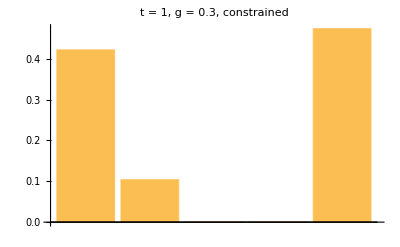

Starting calculations for reversed state... {0.509541-0.462996 ⅈ,8.88404×10^-10+1.6176×10^-9 ⅈ,7.81703×10^-10,0.11925+0.299649 ⅈ,0.375867+0.529827 ⅈ}

returned state (steps = 1) : |st> = (0.38132-0.595396 ⅈ
4.78387×10^-10+1.94523×10^-9 ⅈ
5.12065×10^-10+3.41808×10^-10 ⅈ
-0.00642188+0.0188002 ⅈ
0.00614707-0.706871 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 2.53176×10^6+1.15563×10^-10 ⅈ

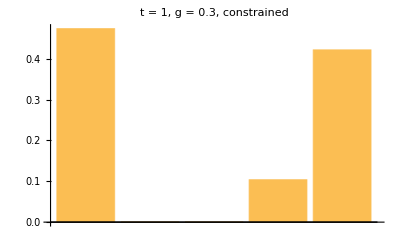

It is superposition of initialState and reversedInitialState, (qfi = :1.37698×10^6) :

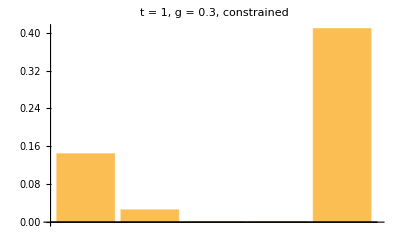

Starting calculations for superposition of initialState and reversed initialState... {0.378594-0.0327848 ⅈ,0.0596248+0.149824 ⅈ,6.46884×10^-10+1.70904×10^-10 ⅈ,-0.00321094+0.00940011 ⅈ,0.257844-0.584934 ⅈ}

returned state (steps = 69) : |st> = (0.507396+0.405656 ⅈ
0.136681+0.292075 ⅈ
-1.47519×10^-10-2.28176×10^-10 ⅈ
0
0.386129-0.570006 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 2.86297×10^6

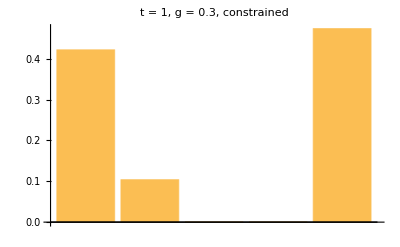

********************

time = 1.25

Starting calculations for initialState...

returned state (steps = 15) : |st> = (0.480995+0.335139 ⅈ
-0.0392408+0.143787 ⅈ
-0.295529-0.24078 ⅈ
0.401663+0.326653 ⅈ
0.275038+0.380943 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 106582.

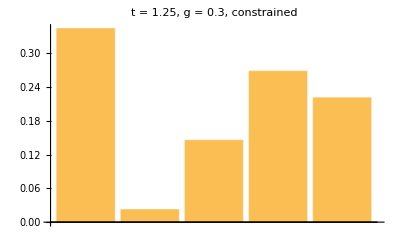

Starting calculations for reversed state... {0.275038+0.380943 ⅈ,0.401663+0.326653 ⅈ,-0.295529-0.24078 ⅈ,-0.0392408+0.143787 ⅈ,0.480995+0.335139 ⅈ}

returned state (steps = 1) : |st> = (0.382314-0.383992 ⅈ
0.160031-0.148256 ⅈ
0.196558+0.396701 ⅈ
0.37392-0.388517 ⅈ
0.338693-0.239405 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 24574.6

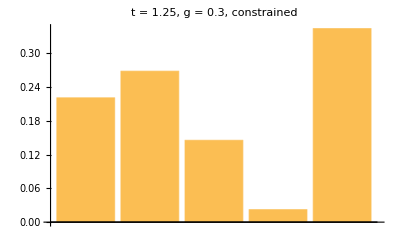

It is superposition of initialState and reversedInitialState, (qfi = :40301.6) :

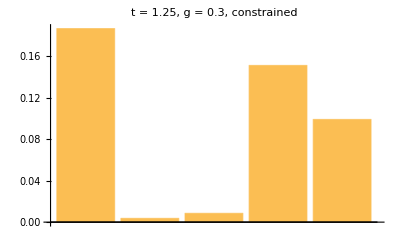

Starting calculations for superposition of initialState and reversed initialState... {0.431655-0.0244262 ⅈ,0.0603952-0.00223435 ⅈ,-0.0494855+0.0779603 ⅈ,0.387791-0.0309318 ⅈ,0.306866+0.0707691 ⅈ}

returned state (steps = 10) : |st> = (0.429353-0.399162 ⅈ
0.0321684-0.145532 ⅈ
0.267819-0.271266 ⅈ
-0.303306-0.419572 ⅈ
0.193028+0.428374 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 106582.

-Graphics-

********************

time = 1.5

Starting calculations for initialState...

returned state (steps = 11) : |st> = (-0.441894+0.350272 ⅈ
-0.121545+0.147559 ⅈ
-0.406017-0.0948347 ⅈ
0.48872-0.178839 ⅈ
-0.354722-0.273844 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 59023.4

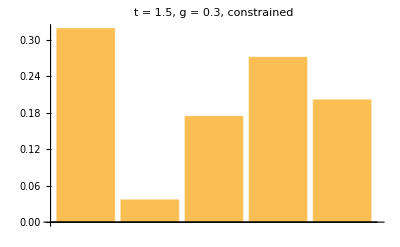

Starting calculations for reversed state... {-0.354722-0.273844 ⅈ,0.48872-0.178839 ⅈ,-0.406017-0.0948347 ⅈ,-0.121545+0.147559 ⅈ,-0.441894+0.350272 ⅈ}

returned state (steps = 1) : |st> = (-0.0533983-0.533305 ⅈ
0.179017-0.16963 ⅈ
-0.32702+0.29184 ⅈ
0.160157-0.508523 ⅈ
0.336611+0.249492 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+2.77556×10^-17 ⅈ, qfi = 20857.5

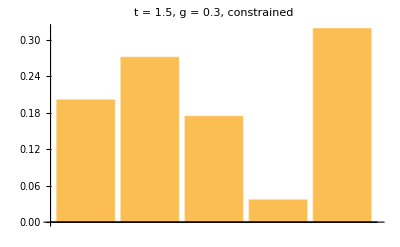

It is superposition of initialState and reversedInitialState, (qfi = :13999.1) :

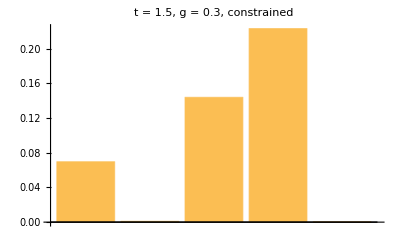

Starting calculations for superposition of initialState and reversed initialState... {-0.247646-0.0915166 ⅈ,0.0287359-0.0110359 ⅈ,-0.366519+0.0985024 ⅈ,0.324439-0.343681 ⅈ,-0.00905545-0.0121759 ⅈ}

returned state (steps = 8) : |st> = (0.153222+0.542762 ⅈ
0.0267536-0.188848 ⅈ
-0.416976+0.000287496 ⅈ
0.0498768+0.518041 ⅈ
-0.412579+0.174953 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 59023.3

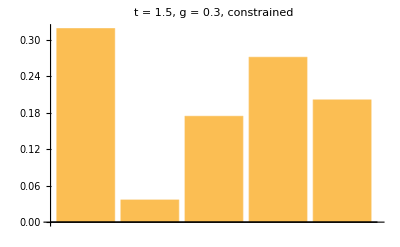

********************

time = 1.75

Starting calculations for initialState...

returned state (steps = 14) : |st> = (-0.326499-0.458702 ⅈ
-0.218881-0.0624444 ⅈ
-0.395204-0.0346654 ⅈ
0.410664+0.305151 ⅈ
0.0924483+0.451094 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 1.2953×10^6-4.00007×10^-10 ⅈ

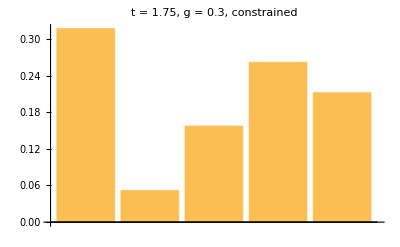

Starting calculations for reversed state... {0.0924483+0.451094 ⅈ,0.410664+0.305151 ⅈ,-0.395204-0.0346654 ⅈ,-0.218881-0.0624444 ⅈ,-0.326499-0.458702 ⅈ}

returned state (steps = 1) : |st> = (-0.140717+0.520051 ⅈ
-0.194016+0.161483 ⅈ
-0.0261799+0.432294 ⅈ
-0.521486-0.02739 ⅈ
-0.356794-0.241791 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+6.93889×10^-18 ⅈ, qfi = 581094.

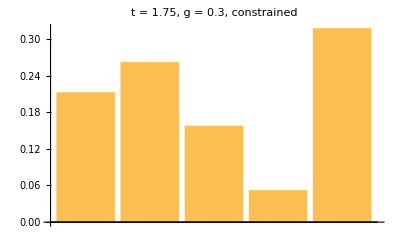

It is superposition of initialState and reversedInitialState, (qfi = :193354.) :

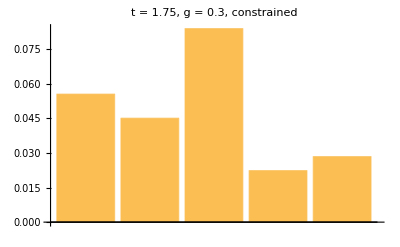

Starting calculations for superposition of initialState and reversed initialState... {-0.233608+0.0306743 ⅈ,-0.206449+0.0495193 ⅈ,-0.210692+0.198815 ⅈ,-0.0554112+0.138881 ⅈ,-0.132173+0.104652 ⅈ}

returned state (steps = 16) : |st> = (0.0110413+0.562928 ⅈ
0.114232-0.196874 ⅈ
-0.39096-0.0673642 ⅈ
0.241823+0.45087 ⅈ
0.372482-0.270721 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 1.2953×10^6

-Graphics-

********************

time = 2.

Starting calculations for initialState...

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

returned state (steps = 100) : |st> = (-0.703722-0.0690902 ⅈ
0.00169862+0.000534097 ⅈ
0
-5.36897×10^-9-6.70127×10^-9 ⅈ
0.690149-0.153929 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 7.07406×10^7+1.83588×10^-9 ⅈ

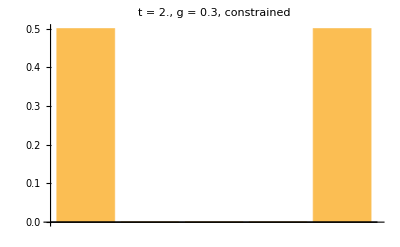

Starting calculations for reversed state... {0.690149-0.153929 ⅈ,-5.36897×10^-9-6.70127×10^-9 ⅈ,0,0.00169862+0.000534097 ⅈ,-0.703722-0.0690902 ⅈ}

returned state (steps = 1) : |st> = (-0.636396-0.308221 ⅈ
-6.10492×10^-9+5.40881×10^-9 ⅈ
0
0.0000413496+0.0000794398 ⅈ
-0.54017+0.456308 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 7.07404×10^7

-Graphics-

It is superposition of initialState and reversedInitialState, (qfi = :7.61186×10^6-1.16428×10^-10 ⅈ) :

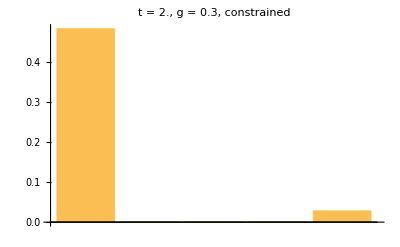

Starting calculations for superposition of initialState and reversed initialState... {-0.670059-0.188656 ⅈ,0.000849306+0.000267051 ⅈ,0,0.0000206721+0.0000397166 ⅈ,0.0749896+0.15119 ⅈ}

returned state (steps = 17) : |st> = (-0.697168-0.118136 ⅈ
-0.000357876+0.0000719126 ⅈ
0
-5.50666×10^-10
0.671334-0.22206 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 7.07406×10^7+1.86152×10^-9 ⅈ

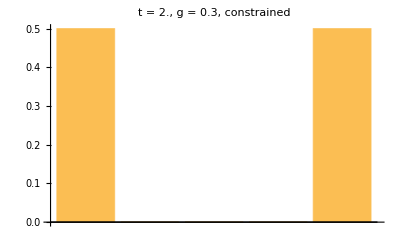

********************

time = 2.25

Starting calculations for initialState...

returned state (steps = 14) : |st> = (-0.485702+0.284366 ⅈ
-0.0666834-0.218246 ⅈ
0.117617-0.379018 ⅈ
-0.362629-0.360843 ⅈ
0.386714+0.249817 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 1.86701×10^6-1.09594×10^-10 ⅈ

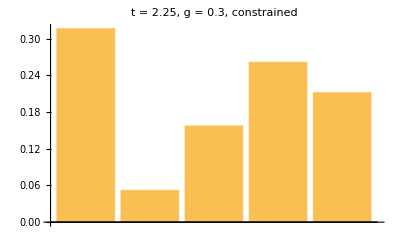

Starting calculations for reversed state... {0.386714+0.249817 ⅈ,-0.362629-0.360843 ⅈ,0.117617-0.379018 ⅈ,-0.0666834-0.218246 ⅈ,-0.485702+0.284366 ⅈ}

returned state (steps = 1) : |st> = (0.186257+0.505518 ⅈ
-0.198289-0.156441 ⅈ
-0.10082-0.421151 ⅈ
0.383895+0.353864 ⅈ
0.349687-0.252106 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 840920.

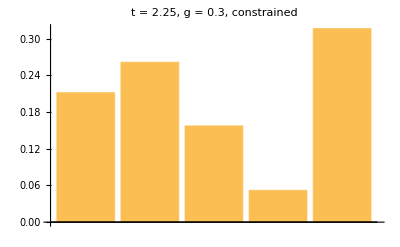

It is superposition of initialState and reversedInitialState, (qfi = :65620.5) :

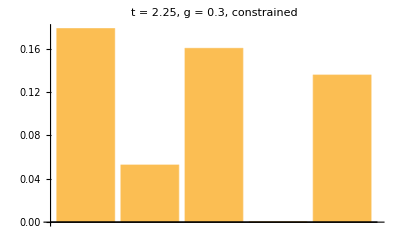

Starting calculations for superposition of initialState and reversed initialState... {-0.149723+0.394942 ⅈ,-0.132486-0.187343 ⅈ,0.00839829-0.400085 ⅈ,0.010633-0.00348909 ⅈ,0.368201-0.00114455 ⅈ}

returned state (steps = 9) : |st> = (0.47682-0.299021 ⅈ
-0.0608976+0.219931 ⅈ
-0.0729592-0.390084 ⅈ
0.458786-0.226325 ⅈ
-0.225063-0.401625 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 1.86701×10^6-1.43643×10^-10 ⅈ

-Graphics-

********************

time = 2.5

Starting calculations for initialState...

returned state (steps = 10) : |st> = (-0.337139+0.425006 ⅈ
0.180221+0.173494 ⅈ
0.186381+0.387016 ⅈ
0.487287+0.169119 ⅈ
0.388711+0.203623 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 522056.+1.10667×10^-10 ⅈ

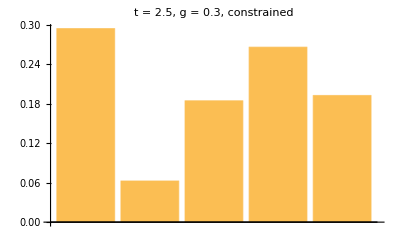

Starting calculations for reversed state... {0.388711+0.203623 ⅈ,0.487287+0.169119 ⅈ,0.186381+0.387016 ⅈ,0.180221+0.173494 ⅈ,-0.337139+0.425006 ⅈ}

returned state (steps = 1) : |st> = (-0.517362-0.107236 ⅈ
-0.0445117+0.267852 ⅈ
-0.0755672-0.434058 ⅈ
-0.510461-0.11561 ⅈ
0.160916+0.391362 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 275416.

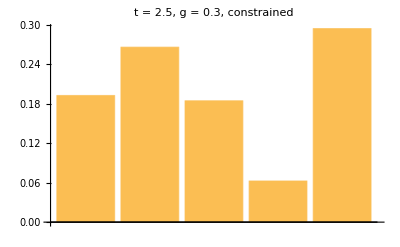

It is superposition of initialState and reversedInitialState, (qfi = :5760.12) :

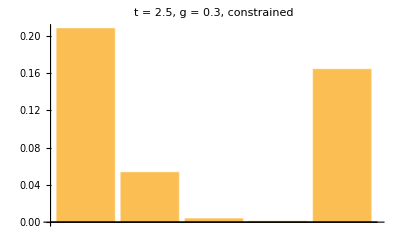

Starting calculations for superposition of initialState and reversed initialState... {-0.427251+0.158885 ⅈ,0.0678548+0.220673 ⅈ,0.055407-0.0235208 ⅈ,-0.011587+0.0267542 ⅈ,0.274813+0.297493 ⅈ}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

returned state (steps = 17) : |st> = (0.506606+0.194058 ⅈ
-0.241523-0.064979 ⅈ
-0.426478-0.0513788 ⅈ
0.255186-0.448255 ⅈ
0.193577+0.393812 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 522056.

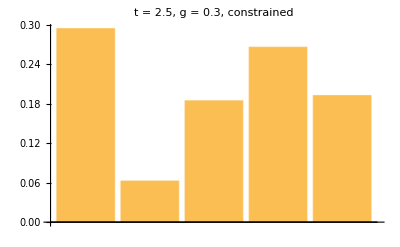

********************

time = 2.75

Starting calculations for initialState...

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

returned state (steps = 12) : |st> = (-0.477293+0.279673 ⅈ
0.101563+0.232262 ⅈ
0.347048+0.203669 ⅈ
0.410298+0.301536 ⅈ
0.266988+0.370458 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 7.61068×10^6-1.19473×10^-9 ⅈ

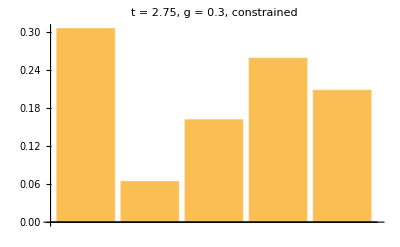

Starting calculations for reversed state... {0.266988+0.370458 ⅈ,0.410298+0.301536 ⅈ,0.347048+0.203669 ⅈ,0.101563+0.232262 ⅈ,-0.477293+0.279673 ⅈ}

returned state (steps = 1) : |st> = (-0.51019+0.177905 ⅈ
-0.182443+0.17068 ⅈ
-0.433586-0.00602983 ⅈ
0.394144-0.336982 ⅈ
-0.412253-0.13692 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 4.01397×10^6-1.2443×10^-10 ⅈ

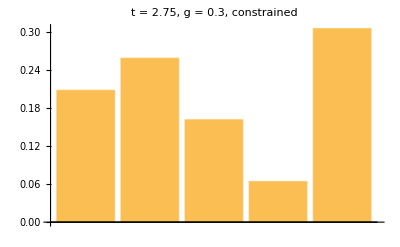

It is superposition of initialState and reversedInitialState, (qfi = :1.08873×10^6) :

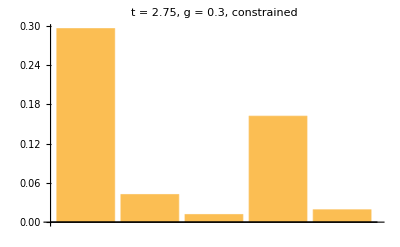

Starting calculations for superposition of initialState and reversed initialState... {-0.493742+0.228789 ⅈ,-0.0404399+0.201471 ⅈ,-0.0432692+0.0988194 ⅈ,0.402221-0.0177227 ⅈ,-0.0726326+0.116769 ⅈ}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

returned state (steps = 14) : |st> = (-0.526702-0.169145 ⅈ
0.173496-0.184824 ⅈ
0.360971+0.177829 ⅈ
0.462221-0.213589 ⅈ
0.289166-0.353419 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 7.61068×10^6-2.10093×10^-10 ⅈ

-Graphics-

********************

time = 3.

Starting calculations for initialState...

returned state (steps = 100) : |st> = (0.118825+0.697051 ⅈ
-0.0000472721-0.000097795 ⅈ
0
0
-0.638759+0.303293 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 4.07265×10^8-3.72498×10^-9 ⅈ

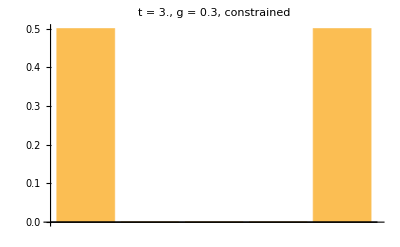

Starting calculations for reversed state... {-0.638759+0.303293 ⅈ,0,0,-0.0000472721-0.000097795 ⅈ,0.118825+0.697051 ⅈ}

returned state (steps = 1) : |st> = (-0.0440761+0.705732 ⅈ
-5.83332×10^-9-9.86649×10^-10 ⅈ
-1.98666×10^-10-2.9402×10^-10 ⅈ
-6.88099×10^-6-5.01955×10^-6 ⅈ
-0.634519+0.312066 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 4.07265×10^8+1.86246×10^-8 ⅈ

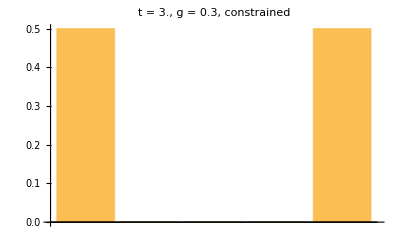

It is superposition of initialState and reversedInitialState, (qfi = :4.04528×10^8-2.98022×10^-8 ⅈ) :

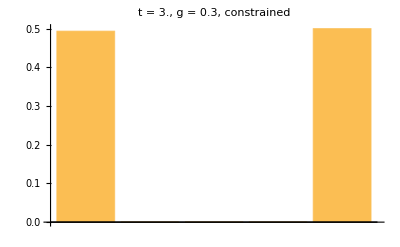

Starting calculations for superposition of initialState and reversed initialState... {0.0373746+0.701392 ⅈ,-0.000023639-0.000048898 ⅈ,-9.93331×10^-11-1.4701×10^-10 ⅈ,-3.44049×10^-6-2.50977×10^-6 ⅈ,-0.636639+0.307679 ⅈ}

returned state (steps = 6) : |st> = (-0.228518-0.669163 ⅈ
6.41857×10^-6+0.0000302161 ⅈ
0
-1.21892×10^-10
-0.707107+0.000124571 ⅈ), <st|st> = 1.+0. ⅈ, <st|n|st> = 2.+0. ⅈ, qfi = 4.07265×10^8-2.98023×10^-8 ⅈ

-Graphics-

********************

Transpose::nmtx: The first two levels of {{1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.},{2.86297×10^6,106582.,59023.4,1.2953×10^6,7.07406×10^7,1.86701×10^6,522056.,7.61068×10^6,4.07265×10^8}} cannot be transposed.

ListLogPlot::lpn: Transpose[{{1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.},{2.86297×10^6,106582.,59023.4,1.2953×10^6,7.07406×10^7,1.86701×10^6,522056.,7.61068×10^6,4.07265×10^8}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

```mathematica
initialState=findInitialState[state5]; 
nBAR=(Length[initialState] - 1)/2;
Print["Initial state is: ", initialState//MatrixForm, "(dim = ", Length[initialState], ")"];
glist=List[(*0.01,*)0.04,0.08,0.3,0.5];
plotsList={};
coefficientsChartList={}; (* list of lists of plots of moduli squared coefficients charts for different time for each iteration of loop (i.e. new list for every g and nbar). Only for N=4 *) 
coefficientsChartRevList={};
coefficientsChartSupList={};
coefficientsChartSupInitialList={};
statesList={};
fishersList={};
fishersRevList={};
fishersSupList={};
fishersSupInitialList={};
SetSharedVariable[initialState,nBAR,glist,plotsList,coefficientsChartList,coefficientsChartRevList,statesList,fishersList,fishersRevList];
Do[
Print["Loop: g = ", glist[[i]]];

(* generate table of qfi and max states for dim[initiaState]-1 -photon state given by Subscript[ψ, 2] *)
fishers={};fishersRev={};fishersSup={};fishersSupInitial={};states={};charts={};chartsRev={};chartsSup={};chartsSupInitial={};
Module[{state,qfi,stepReturned,step=0},
For[tt=1,tt≤3,tt=tt+0.25,
(Print["time = ", tt];

Print["Starting calculations for initialState..."];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},100,0.1,initialState,nBAR]);
stateAfter=state;
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
fishers=Append[fishers,Re[qfi]];
states=Append[states,state];
newChart = BarChart[Abs[stateAfter]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
charts=Append[charts,newChart];
Print[newChart];

(* now lets reverse returned state and check its fisher information *)
revState=Reverse[stateAfter];
Print["Starting calculations for reversed state... ", revState];
(* one step of CalculateOptimalQFI just returns QFI calculated for initial state *)
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},1,0.1,revState,nBAR]; 
stateRevAfter=state;
fishersRev=Append[fishersRev,Re[qfi]];
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
newChartRev = BarChart[Abs[revState]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
Print[newChartRev];
chartsRev=Append[chartsRev,newChartRev];


(* Now lets take a look at their superposition *)
superposition={};
For[el=1,el≤Length[initialState],el++,
superposition=Append[superposition, stateAfter[[el]]/2 + stateRevAfter[[el]]/2];
];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},1,0.1,superposition,nBAR]; 
stateSupInitialAfter=state;
fishersSupInitial=Append[fishersSupInitial,Re[qfi]];
Print["It is superposition of initialState and reversedInitialState, (qfi = :", qfi,") :"];
newChartSupInitial=BarChart[Abs[superposition]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
chartsSupInitial=Append[chartsSupInitial,newChartSupInitial];
Print[newChartSupInitial];

Print["Starting calculations for superposition of initialState and reversed initialState... ", superposition];
{state,qfi,stepReturned}=CalculateOptimalQFI[ {f->0.001, t->(tt+0.0000001)*2*Pi/ωm,g->glist[[i]]},100,0.1,superposition,nBAR];
stateSupAfter=state; 
fishersSup=Append[fishersSup,Re[qfi]];
Print["returned state (steps = ", stepReturned, ") : |st> = ", state//MatrixForm,", <st|st> = ", Conjugate[state].state, ", <st|n|st> = ", Conjugate[state].defineNumberOperator[Length[state]].state, ", qfi = ", qfi];
newChartSup= BarChart[Abs[stateSupAfter]^2,PlotLabel->"t = " <>ToString[ tt]<>", g = " <> ToString[glist[[i]]] <> ", constrained"];
chartsSup=Append[chartsSup,newChartSup];
Print[newChartSup];
Print["\n\n\n********************"];
];
];
    
(* generate x axis - time *)
timeArray=Table[1+0.05*i,{i,0,40}];
plot=ListLogPlot[
Transpose@{timeArray,fishers},
PlotRange->{{0.6,3.5},Automatic},
PlotLabels->{"dim=" <> ToString[Length[initialState]]},
AxesLabel->{"time", "QFI"},
PlotLabel->"dim="<>ToString[Length[initialState]]<>", g="<>ToString[glist[[i]]] <> ", constraints: <ψ|ψ>=1 && <ψ|n|ψ>=N/2" ,LabelStyle->{GrayLevel[0]}
];
coefficientsChartList=Append[coefficientsChartList,charts];
plotsList=Append[plotsList,plot];
statesList=Append[statesList,states];
fishersList=Append[fishersList,fishers];
fishersRevList=Append[fishersRevList,fishersRev];
fishersSupList=Append[fishersSupList,fishersSup];
fishersSupInitialList=Append[fishersSupInitialList,fishersSupInitial];
coefficientsChartRevList=Append[coefficientsChartRevList,chartsRev];
coefficientsChartSupList=Append[coefficientsChartSupList,chartsSup];
coefficientsChartSupInitialList=Append[coefficientsChartSupInitialList,chartsSupInitial];

,
{i,3,3}
]
dir=FileNameJoin[{NotebookDirectory[],"noweobrazki"}];
Switch[FileType[dir],
None,CreateDirectory[dir] (*create dir*),
Directory,Null (*do nothing*),
File,Print["File with same name already exists!!"] (*error!*)
];
Table[
Export[
FileNameJoin[
{dir,StringJoin["qfi_vs_time_g_", ToString[glist[[i]]],".jpg"]}
],
plotsList[[i]],"JPEG"
],
{i,Length[plotsList]}
];
```

```mathematica
'
```

```mathematica
pDim5Nbar2G03=plotsList[[2]](*=Show[plotsList[[1]],ImageSize->Medium]*)
```

-Graphics-

```mathematica
pDim5Nbar25G03;
pDim5Nbar2G03;
Show[pDim5Nbar25G03, pDim5Nbar2G03, PlotStyle->{Red,Blue},ImageSize->Medium]
```

-Graphics-

```mathematica
Show[plotsList[[1]],ImageSize->Medium]
Show[plotsList[[2]],ImageSize->Medium]
Show[plotsList[[3]],ImageSize->Medium]
Show[plotsList[[4]],ImageSize->Medium]
Show[plotsList[[5]],ImageSize->Medium]
```

```mathematica
(* Eksport wykresów QFI(t) *)
For[i=1,i≤Length[plotsList],i++,
Export[FileNameJoin[{dir,StringJoin["qfi_vs_time_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[i]]*100],10,3],"_constrained_nbar.jpg"]}],plotsList[[i]],"JPEG"]
]
```

```mathematica
(* Eksport histogramów współczynników *)
For[gg=1,gg≤Length[coefficientsChartList],gg++,
For[tt=1;jj=1,tt≤3,tt+=0.25;jj+=1,
Export[FileNameJoin[{dir,StringJoin["coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["rev_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartRevList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["sup_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartSupList[[gg]][[jj]],"JPEG"];
Export[FileNameJoin[{dir,StringJoin["supInitial_coefficients_dim_",ToString[Length[initialState]],"_g_", IntegerString[IntegerPart[glist[[gg]]*100],10,3],"_t_",IntegerString[IntegerPart[tt*100],10,3],"_constrained_nbar.jpg"]}],coefficientsChartSupInitialList[[gg]][[jj]],"JPEG"];
];
]
```

```mathematica
(*saving lists of all coefficients here *)
coefficientsDim5g05=coefficientsChartList[[1]];
coefficientsDim5g03=coefficientsChartList[[2]];
coefficientsDim5g004=coefficientsChartList[[3]];
coefficientsDim5g008=coefficientsChartList[[4]];
```

```mathematica
coefficientsChartList[[1]]
```

Part::partd: Part specification coefficientsChartList⟦1⟧ is longer than depth of object.

coefficientsChartList⟦1⟧

### Derivation of spin-squeezed state formula and finding θ which maximizes QFI

In this part, we do not fully optimize state over all possible coefficients – we study
the dependence of Quantum Fisher information over squeezing parameter (squeezing
“force”) and squeezing angle for a class of states called spin-squeezed states. We start
with a state |0> ⊗ |N>, and then create a spin-squeezed state: |ψ_(a, θ)> 
	* a – squeezing parameter
	* θ – squeezing angle
as follows:
|ψ_(a, θ)> = ⅇ^(i J_y π/2) ⅇ^(−iθ J_z) ⅇ^(a((J_+)^2−(J_-)^2)) |0> ⊗ |N>

Here, we use the angular momentum notation for the states |n> ⊗ |N − n>. The total
angular momentum is equal to N/2 and the state |n> ⊗ |N − n> can be associated with
angular momentum state |J = N/2, Jz = n − N/2>.
The meaning of every operator acting on the state in Eq. 16 is as follows:
	1. ⅇ^(a((J_+)^2−(J_-)^2)) is a two-axis twisting operation with strength a
	2. ⅇ^(−iθ J_z) is a rotation with respect to z-axis, which introduces the squeezing angle θ
	3. ⅇ^(i J_y π/2) is a rotation with respect to y-axis by 90 degrees which moves the state from the pole to the equator of the Bloch sphere
		
Then we calculate Quantum Fisher Information for the state|ψ_(a, θ)> fed into the
interferometer, i.e. for Λ(|ψ_(a, θ)><ψ_(a, θ)|) (note that for the spin-squeezed states we no
longer use the global optimization algorithm). Below in Fig. 4 we plot the squeezing
angle for which the QFI is maximal. Again, we use the following parameter values:
ω_0 = 10, ω_m = 0.1, f = 0.001

Lets create matrices for J_+ and J_-: (n is dimension, i.e.: 2j+1)

```mathematica
SubMinus[J][n_]:=Module[{l=(n-1)/2},Table[√(l (l+1.)-m (m-1.)) KroneckerDelta[mp,m-1],{mp,-l,l},{m,-l,l}]];
SubPlus[J][n_]:=Module[{l=(n-1)/2},Table[√(l (l+1.)-m (m+1.)) KroneckerDelta[mp,m+1],{mp,-l,l},{m,-l,l}]];
```

Now we can define J_x and J_y:

```mathematica
Subscript[J, x][n_]:=(SubPlus[J][n]+SubMinus[J][n])/2.;
Subscript[J, y][n_]:=(SubPlus[J][n]-SubMinus[J][n])/(2.*ⅈ);
```

Because J_z|j,m>=m|j,m>, we can define J_z matrix as:

```mathematica
Subscript[J, z][n_]:=Array[If[#2-#1==0,#1-1-(n-1.)/2.,0.]&,{n,n}];
```

Now we define first operator, the two axis twisting with strength a:

```mathematica
FirstOperator[n_,a_]:=MatrixExp[a(SubPlus[J][n].SubPlus[J][n]-SubMinus[J][n].SubMinus[J][n])];
```

Rotation by θ with respect to z axis:

```mathematica
SecondOperator[n_,θ_]:=MatrixExp[-ⅈ θ Subscript[J, z][n]];
```

And rotation by π/2 from the pole to the equator of Bloch sphere around y axis:

```mathematica
ThirdOperator[n_]:=MatrixExp[-ⅈ*(Pi/2)*Subscript[J, y][n]];
```

We having all these three parts we can define spin squeezed state |ψ_(a, θ)>:

```mathematica
ψ2[a_,θ_,n_]:= ThirdOperator[n].SecondOperator[n,θ]. FirstOperator[n,a].Array[If[#==1,1.,0.]&,n];
```

In order to find optimal squeezing angle θ we will construct the function FindθMaximizingQFI which will check θ in range [0,π/2] , calculate Fisher information using our algorithm for each of them and return the angle maximizing the QFI. 
Parameters:
■ rules - set of rules which can contain e.g. parameter values for used input state
■ a - squeezing force
■ nθ - number of θ to check in range [0,π/2] 
■ dimension for rotation generators ( |2j+1| )

```mathematica
FindθMaximizingQFI[rules_,a_,nθ_,n_]:=(
Print[rules];
fisherVsθ=Re[Array[CalculateQFI[rules,ψ2[a,#,n],n/2][[2]]&,nθ,{0,π/2}]];
maxIndex=Position[fisherVsθ,Max[fisherVsθ]][[1,1]];

(* return *)(maxIndex-1)/(nθ-1)π/2
);
```

```mathematica
n=5;
QFIforVariousG = {};
For[gg=0.01,gg≤0.2,gg=gg+0.02,
Print["gg = ",gg];

p=DiscretePlot[
	CalculateQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},ψ2[0.05,θ,n],n/2][[2]],
	{θ,0,2*Pi,0.02},
	Joined->False,
	Filling->None,
	Frame->{{True,False},{True,False}},
	FrameLabel->{Style["squeezing angle θ"],Style["QFI"]},
	(*AxesLabel->{HoldForm[squeezing angle θ],HoldForm[QFI]},*)
	PlotLabel-> "QFI vs θ for g = " <> ToString[gg],
	(*PlotLegends->{"g = "<>ToString[gg]},*)
	Filling->None
];
QFIforVariousG=Append[QFIforVariousG,p];
(*Print[p];*)
]
```

```mathematica
QFIforVariousG[[1]]
```

-Graphics-

```mathematica
Clear[g];
```

```mathematica
ω0
ωm=0.1
```

10.

0.1

aa = 0.05

{t→94.2478,g→0.01,f→0.001}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1-(x1-ⅈ y1) (x1+ⅈ y1)-(x2-ⅈ y2) (x2+ⅈ y2)-(x3-ⅈ y3) (x3+ⅈ y3)-(x4-ⅈ y4) (x4+ⅈ y4)-(x5-ⅈ y5) (x5+ⅈ y5)==0,5/2-(x2-ⅈ y2) (x2+ⅈ y2)-2 (x3-ⅈ y3) (x3+ⅈ y3)-3 (x4-ⅈ y4) (x4+ⅈ y4)-4 (x5-ⅈ y5) (x5+ⅈ y5)==0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

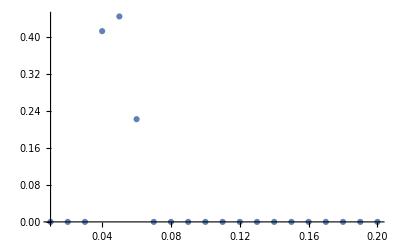

aa = 0.1

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

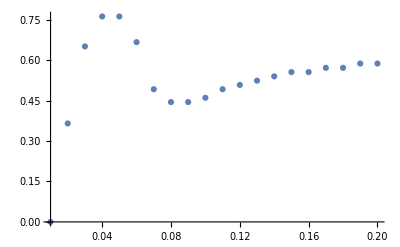

aa = 0.15

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

{t→94.2478,g→0.16,f→0.001}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

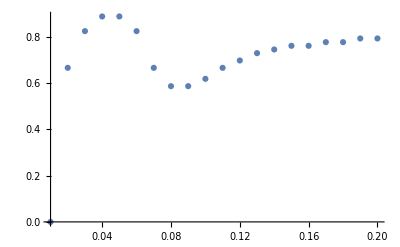

aa = 0.2

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

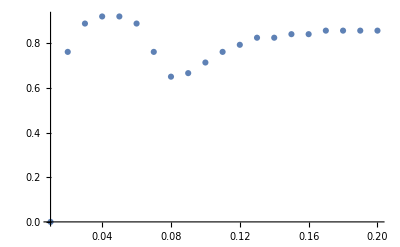

aa = 0.25

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

{t→94.2478,g→0.11,f→0.001}

{t→94.2478,g→0.12,f→0.001}

{t→94.2478,g→0.13,f→0.001}

{t→94.2478,g→0.14,f→0.001}

{t→94.2478,g→0.15,f→0.001}

{t→94.2478,g→0.16,f→0.001}

{t→94.2478,g→0.17,f→0.001}

{t→94.2478,g→0.18,f→0.001}

{t→94.2478,g→0.19,f→0.001}

{t→94.2478,g→0.2,f→0.001}

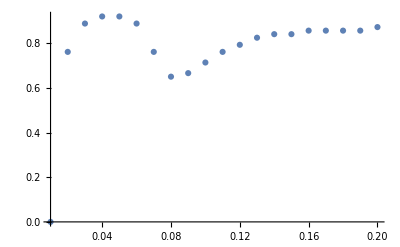

aa = 0.3

{t→94.2478,g→0.01,f→0.001}

{t→94.2478,g→0.02,f→0.001}

{t→94.2478,g→0.03,f→0.001}

{t→94.2478,g→0.04,f→0.001}

{t→94.2478,g→0.05,f→0.001}

{t→94.2478,g→0.06,f→0.001}

{t→94.2478,g→0.07,f→0.001}

{t→94.2478,g→0.08,f→0.001}

{t→94.2478,g→0.09,f→0.001}

{t→94.2478,g→0.1,f→0.001}

$Aborted

```mathematica
valuesForVariousA = {};
plotsForVariousA2={};
For[aa=0.05,aa≤0.3,aa=aa+0.05,
Print["aa = ", aa];
(*values=Table[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.01}];*)
p=DiscretePlot[
FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],
{gg,0.01,0.2,0.01},
Joined->False,
Filling->None
(*PlotRange->{{0,0.15},{0,1.3}}*)
(*AxesLabel->{"Value of g","θ[rad] s.t. QFI is maximal"},
PlotLegends->{"a = " <> ToString[aa]}*)
];
Print[p];
(*p=□DiscretePlot[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.001},Joined->False,Filling->None,PlotRange->{{0,0.15},{0,1.3}},AxesLabel->{"Value of g","optymalny kąt / pi"},PlotLegends->"t=1.5, a=0.05"]*);
plotsForVariousA2=Append[plotsForVariousA2,p];
(*valuesForVariousA = Append[valuesForVariousA,values];*)
];
```

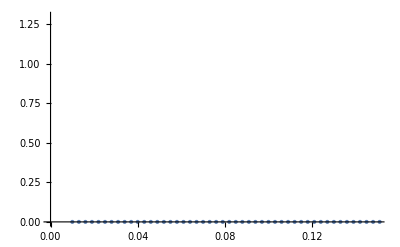

```mathematica
p
```

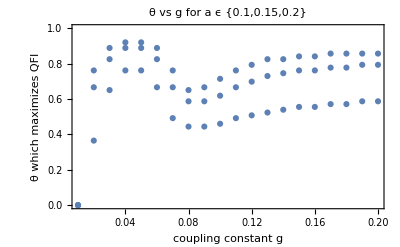

```mathematica
plotsForVariousA2;
Show[(*plotsForVariousA2[[1]],*)plotsForVariousA2[[2]],plotsForVariousA2[[3]],plotsForVariousA2[[4]],
AxesLabel->{HoldForm[coupling constant g],
HoldForm[θ which maximizes QFI]},
PlotLabel->HoldForm[θ vs g for a ϵ {0.1,0.15,0.2}],
PlotLabels->{"a=0.1","a=0.15","a=0.2"},	
Frame->{{True,False},{True,False}},
PlotRange->{0,1.0},
FrameLabel->{Style["coupling constant g"],Style["θ which maximizes QFI"]}]
```

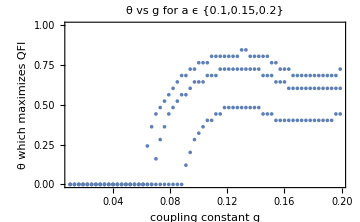

```mathematica
Show[%477,ImageSize->Medium]
```

```mathematica
plotsForVariousA2={};
multiplotList={};
For[i=0,i<3,i++,
Switch[i,
0,currentnbar=0,
1,currentnbar=1,
2,currentnbar=2];

For[aa=0.05,aa≤0.3,aa=aa+0.05,
Print["i = ", i, ", aa = ", aa];
(*values=Table[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.01}];*)
Print["Plot title will be ", "θ vs g for a ϵ {0.05`,0.1`,0.15`,0.2`}, nbar = "<> ToString[currentnbar]];
p=DiscretePlot[
FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001,nbar->currentnbar},aa,100,5],
{gg,0.01,0.2,0.003},
Joined->False,
Filling->None,
PlotRange->{{0,0.15},{0,1.3}}
(*AxesLabel->{"Value of g","θ[rad] s.t. QFI is maximal"},
PlotLegends->{"a = " <> ToString[aa]}*)
];
Print[p];
(*p=□DiscretePlot[FindθMaximizingQFI[{t->1.5*2*Pi/ωm,g->gg,f->0.001},aa,100,5],{gg,0.01,0.15,0.001},Joined->False,Filling->None,PlotRange->{{0,0.15},{0,1.3}},AxesLabel->{"Value of g","optymalny kąt / pi"},PlotLegends->"t=1.5, a=0.05"]*);
plotsForVariousA2=Append[plotsForVariousA2,p]
(*valuesForVariousA = Append[valuesForVariousA,values];*)
];


s=Show[plotsForVariousA2[[1]],plotsForVariousA2[[2]],plotsForVariousA2[[3]],plotsForVariousA2[[4]],
AxesLabel->{HoldForm[coupling constant g],
HoldForm[θ which maximizes QFI]},
PlotLabel->"θ vs g for a ϵ {0.05`,0.1`,0.15`,0.2`}, nbar = "<> ToString[currentnbar],	
Frame->{{True,False},{True,False}},
FrameLabel->{Style["coupling constant g"],Style["θ which maximizes QFI"]}];
multiplotList=Append[multiplotList,s];
s
]
```

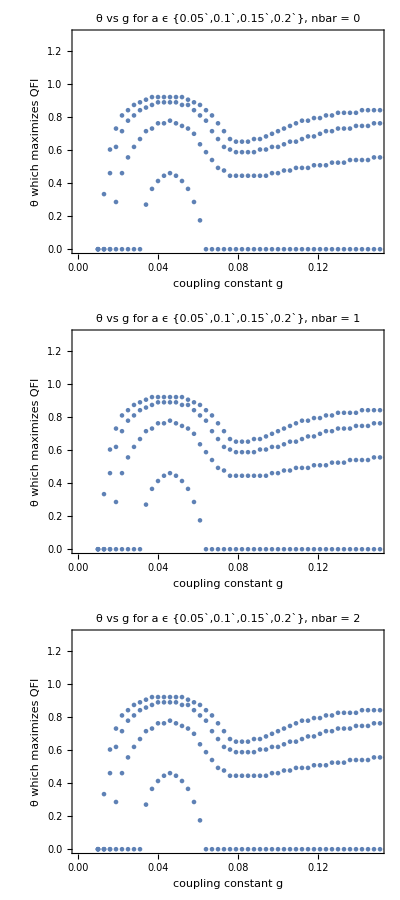
(-Graphics-)

```mathematica
multiplotList
```

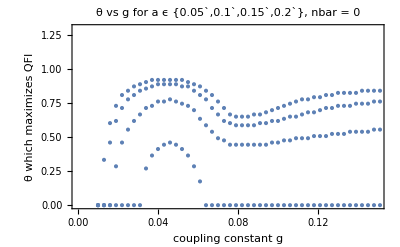

```mathematica
show1=multiplotList[[1]]
```

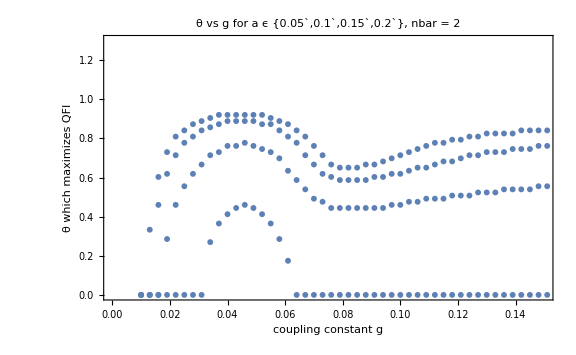

```mathematica
Show[multiplotList[[3]],ImageSize->Large]
```

### Analysis of plots in order to find optimal θ

plan minimum dajemy dekoherencje i patrzymy co sie dzieje

przechodzac do granicy chcemy odtwarzac to co oni maja do czynienia w detektorze

u nas mamy statyczne przesuniecie, a nas interesuje jak nasza amplituda sie przenosi na lustro i swiatlo
te modele prawdziwsze juz istnieją ale są robione ze swiatlem polklasycznym (tylko troche domieszki kwantowosci), a my chcemy calkiem kwantowo